### Normal Coords / EF Coords

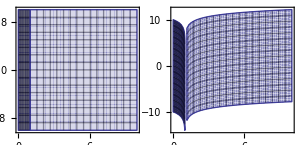

```mathematica
tEFI[t_,r_] := t+Log[1-r];
tEFO[t_,r_] := t+Log[r-1];
GraphicsGrid[{{
Show[
ParametricPlot[{r,t},{t,-10,10},{r,0,1},PlotRange->All,AspectRatio->Full],
ParametricPlot[{r,t},{t,-10,10},{r,1,10},PlotRange->All,AspectRatio->Full]
],
Show[
ParametricPlot[{r,tEFI[t,r]},{t,-10,10},{r,0,1},PlotRange->All,AspectRatio->Full],
ParametricPlot[{r,tEFO[t,r]},{t,-10,10},{r,1,10},PlotRange->All,AspectRatio->Full]
]
}},ImageSize->300]
```

### Rotated EF - Different rotations for inside & Outside

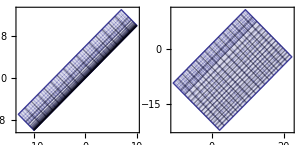

```mathematica
uI[t_,r_] := tEFI[t,r]-r-2 Log[1-r];
vI[t_,r_] := tEFI[t,r]+r;
uO[t_,r_] := tEFO[t,r]-r-2 Log[r-1];
vO[t_,r_] := tEFO[t,r]+r;
GraphicsGrid[{{
ParametricPlot[{vI[t,r],uI[t,r]},{t,-10,10},{r,0,1},PlotRange->All,AspectRatio->Full],
ParametricPlot[{vO[t,r],uO[t,r]},{t,-10,10},{r,1,10},PlotRange->All,AspectRatio->Full]
}},ImageSize->300]
```

### Infinities brought in

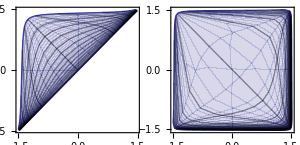

```mathematica
UI[t_,r_] := ArcTan[uI[t,r]];
VI[t_,r_] := ArcTan[vI[t,r]];
UO[t_,r_] := ArcTan[uO[t,r]];
VO[t_,r_] := ArcTan[vO[t,r]];
GraphicsGrid[{{
ParametricPlot[{VI[t,r],UI[t,r]},{t,-10,10},{r,0,1},PlotRange->All,AspectRatio->Full],
ParametricPlot[{VO[t,r],UO[t,r]},{t,-10,10},{r,1.001,10},PlotRange->All,AspectRatio->Full]
}},ImageSize->300]
```

### Rotate Back

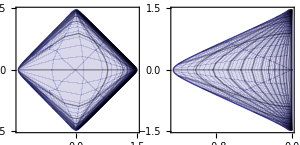

```mathematica
TI[t_,r_] := (VI[t,r]+UI[t,r])/2;
RI[t_,r_] := (VI[t,r]-UI[t,r])/2;
TO[t_,r_] := (VO[t,r]+UO[t,r])/2;
RO[t_,r_] := (VO[t,r]-UO[t,r])/2;
GraphicsGrid[{{
ParametricPlot[{RO[t,r],TO[t,r]},{t,-10,10},{r,1.001,10},PlotRange->All,AspectRatio->Full],
ParametricPlot[{RI[t,r],TI[t,r]},{t,-10,10},{r,0,1},PlotRange->All,AspectRatio->Full]
}},ImageSize->300]
```

### Nicer / lined up figures:

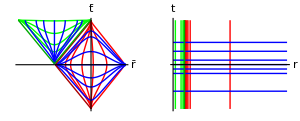

```mathematica
R[t_,r_] := If[r<1,TI[t,r],RO[t,r]];
T[t_,r_] := If[r<1,RI[t,r],TO[t,r]];
ϵ = 10^-9;

GraphicsGrid[{{
Show[
Table[ParametricPlot[{R[t,r],T[t,r]},{t,-100,100},PlotStyle->Red],{r,{1.05,1.1,1.2,1.3,1.5,5}}],
Table[ParametricPlot[{R[t,r],T[t,r]},{r,1+ϵ,10},PlotStyle->Blue],{t,{-3,-1,-.5,0,.5,1.5,2.5}}],
ParametricPlot[{R[t,1+ϵ],T[t,1+ϵ]},{t,-100,100},PlotStyle->{Thick,Darker[Red]}],

Table[ParametricPlot[{R[t,r]-π/2,T[t,r]+π/2},{t,-100,100},PlotStyle->Green],{r,{0.95,.87,0.7,.2}}],
Table[ParametricPlot[{R[t,r]-π/2,T[t,r]+π/2},{r,ϵ,1-ϵ},PlotStyle->Blue],{t,{-3,-1,-.5,0,.5,1.5,2.5}}],
ParametricPlot[{R[t,1-ϵ]-π/2,T[t,1-ϵ]+π/2},{t,-100,100},PlotStyle->{Thick,Darker[Green]}],

PlotRange->All,Ticks->False,AxesLabel->(Style[#,FontSize-> 20]&/@{"r̄","t̄"})
],
Show[
Table[ParametricPlot[{r,t},{t,-5,5},PlotStyle->Red],{r,{1.05,1.1,1.2,1.3,1.5,5}}],
Table[ParametricPlot[{r,t},{r,1,10},PlotStyle->Blue],{t,{-3,-1,-.5,0,.5,1.5,2.5}}],
ParametricPlot[{1,t},{t,-5,5},PlotStyle->{Thick,Darker[Red]}],

Table[ParametricPlot[{r,t},{t,-5,5},PlotStyle->Green],{r,{0.95,.87,0.7,.2}}],
Table[ParametricPlot[{r,t},{r,0,1},PlotStyle->Blue],{t,{-3,-1,-.5,0,.5,1.5,2.5}}],
ParametricPlot[{1,t},{t,-5,5},PlotStyle->{Thick,Darker[Green]}],

PlotRange->All,Ticks->False,AxesLabel->(Style[#,FontSize-> 20]&/@{"r","t"}),AspectRatio->1
]
}},ImageSize->300]
```